# Werning (2012)

ODE

```mathematica
OdeOutputGap[x_]:=σ^-1*(i-r-p)
OdeInflation[p_]:=ρ*p-κ*x
```

Loci

```mathematica
Solve[OdeOutputGap[x]==0,p]
```

{{p→i-r}}

Phase plot

```mathematica
Solve[OdeInflation[p]==0,x]
```

{{x→(p ρ)/κ}}

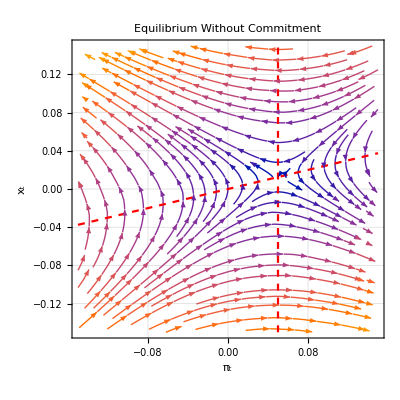

```mathematica
Phase=StreamPlot[({OdeInflation[p],OdeOutputGap[x]}//.{σ->1,i->0,r->-0.05,ρ->0.5,κ->2}),
{p,-0.15,0.15},{x,-0.15,0.15},
FrameLabel-> {"π_t","x_t"},
PlotLabel->"Equilibrium Without Commitment",
GridLines->Automatic,
PlotRange->{{-0.15,0.15},{-0.15,0.15}}];
LocusP=Plot[{(p*ρ)/κ}//.{σ->1,i->0,r->-0.05,ρ->0.5,κ->2},{p,-0.15,0.15},PlotStyle->{Red,Dashed}];
LocusX=ContourPlot[p=={i-r//.{σ->1,i->0,r->-0.05,ρ->0.5,κ->2}},{p,-0.15,0.15},{x,-0.15,0.15},ContourStyle->{Red,Dashed}];
Show[Phase,LocusP,LocusX]
```

```mathematica
Clear["Global`*"]
```

```mathematica
sol=DSolve[{x'[t]==σ^-1(-r-p[t]),p'[t]==ρ*p[t]-κ*x[t],x[5]==0,p[5]==0},{x[t],p[t]},t]//FullSimplify
```

{{p[t]→1/(2 (4 κ+ρ^2 σ))ⅇ^(-((5+t) (ρ √σ+√(4 κ+ρ^2 σ)))/(2 √σ)) r (-2 ⅇ^(((5+t) (ρ √σ+√(4 κ+ρ^2 σ)))/(2 √σ)) (4 κ+ρ^2 σ)+ⅇ^(t (ρ+(√(4 κ+ρ^2 σ))/(√σ))) (4 κ+ρ^2 σ-ρ √σ √(4 κ+ρ^2 σ))+ⅇ^(t ρ+(5 √(4 κ+ρ^2 σ))/(√σ)) (4 κ+ρ^2 σ+ρ √σ √(4 κ+ρ^2 σ))),x[t]→1/(2 κ √σ (4 κ+ρ^2 σ))ⅇ^(-((5+t) (ρ √σ+√(4 κ+ρ^2 σ)))/(2 √σ)) r (-2 ⅇ^(((5+t) (ρ √σ+√(4 κ+ρ^2 σ)))/(2 √σ)) ρ √σ (4 κ+ρ^2 σ)+ⅇ^(t (ρ+(√(4 κ+ρ^2 σ))/(√σ))) (4 κ ρ √σ+ρ^3 σ^(3/2)-2 κ √(4 κ+ρ^2 σ)-ρ^2 σ √(4 κ+ρ^2 σ))+ⅇ^(t ρ+(5 √(4 κ+ρ^2 σ))/(√σ)) (ρ^2 σ (ρ √σ+√(4 κ+ρ^2 σ))+2 κ (2 ρ √σ+√(4 κ+ρ^2 σ))))}}

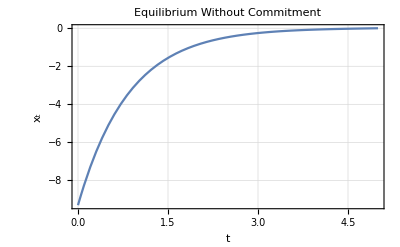

```mathematica
Plot[Evaluate[{{x[t]}/.sol//.{σ->1,i->0,r->-0.05,ρ->0.5,κ->2,T->5}}],{t,0,5},
PlotRange->All,
Frame->True,
FrameLabel-> {"t","x_t"},
PlotLabel->"Equilibrium Without Commitment",
GridLines->Automatic]
```

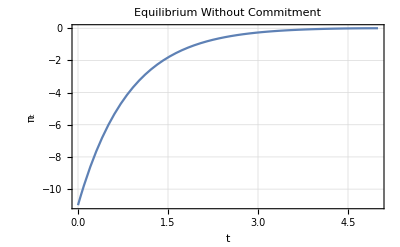

```mathematica
Plot[Evaluate[{{p[t]}/.sol//.{σ->1,i->0,r->-0.05,ρ->0.5,κ->2,T->5}}],{t,0,5},
PlotRange->All,
Frame->True,
FrameLabel-> {"t","π_t"},
PlotLabel->"Equilibrium Without Commitment",
GridLines->Automatic]
```